```mathematica
data=Import["bessel.dat"]
```

{{0.,1.,0.,0.},{1.,0.765198,0.440051,0.114903},{2.,0.223891,0.576725,0.352834},{3.,-0.260052,0.339059,0.486091},{4.,-0.39715,-0.0660433,0.364128},{5.,-0.177597,-0.327579,0.0465651},{6.,0.150645,-0.276684,-0.242873},{7.,0.300079,-0.00468282,-0.301417},{8.,0.171651,0.234636,-0.112992},{9.,-0.0903336,0.245312,0.144847},{10.,-0.245936,0.0434727,0.25463}}

```mathematica
MatrixForm[data]
```

(0. | 1. | 0. | 0.
1. | 0.765198 | 0.440051 | 0.114903
2. | 0.223891 | 0.576725 | 0.352834
3. | -0.260052 | 0.339059 | 0.486091
4. | -0.39715 | -0.0660433 | 0.364128
5. | -0.177597 | -0.327579 | 0.0465651
6. | 0.150645 | -0.276684 | -0.242873
7. | 0.300079 | -0.00468282 | -0.301417
8. | 0.171651 | 0.234636 | -0.112992
9. | -0.0903336 | 0.245312 | 0.144847
10. | -0.245936 | 0.0434727 | 0.25463)

```mathematica
j0=data[[All,2]]
j1=data[[All,3]]
j2=data[[All,4]]
x=data[[All,1]]
```

{1.,0.765198,0.223891,-0.260052,-0.39715,-0.177597,0.150645,0.300079,0.171651,-0.0903336,-0.245936}

{0.,0.440051,0.576725,0.339059,-0.0660433,-0.327579,-0.276684,-0.00468282,0.234636,0.245312,0.0434727}

{0.,0.114903,0.352834,0.486091,0.364128,0.0465651,-0.242873,-0.301417,-0.112992,0.144847,0.25463}

{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

```mathematica
j1p=1/2*(j0-j2)
```

{0.5,0.325147,-0.0644716,-0.373072,-0.380639,-0.112081,0.196759,0.300748,0.142321,-0.11759,-0.250283}

```mathematica
airy=(2*j1[[2;;11]]/x[[2;;11]])^2
```

{0.774578,0.332612,0.0510938,0.00109043,0.0171693,0.008506,1.79011×10^-6,0.00344089,0.00297175,0.0000755952}

0.765198

0.997503

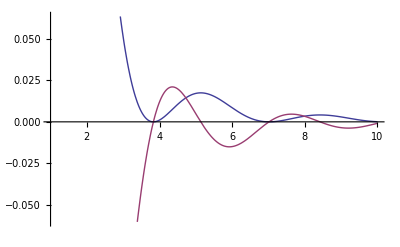

```mathematica
f[x_]:=(2*BesselJ[1,x]/x)^2
BesselJ[0,1.]
f[0.1]
Plot[{f[x],f'[x]},{x,1,10}]
```

```mathematica
f'[0.1]
y=1.;While[y<11,Print[f'[y]];y=y+1]
```

-0.0498959

-0.404507

-0.406976

-0.146501

0.0120241

0.0048812

-0.0149331

-0.000230446

0.003314

-0.00350941

-0.000885558

```mathematica
a={{2,-1,0,0,0},{-1,2,-1,0,0},{0,-1,2,-1,0},{0,0,-1,2,-1},{0,0,0,-1,2}}
b={{0.},{1},{2},{3},{4}}
```

{{2,-1,0,0,0},{-1,2,-1,0,0},{0,-1,2,-1,0},{0,0,-1,2,-1},{0,0,0,-1,2}}

{{0.},{1},{2},{3},{4}}

```mathematica
MatrixForm[a]
MatrixForm[b]
```

(2 | -1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
0 | 0 | 0 | -1 | 2)

(0
1
2
3
4)

```mathematica
κ=LinearSolve[a,b];
MatrixForm[κ]
```

(3.33333
6.66667
9.
9.33333
6.66667)